```mathematica
Clear[Fitto1];
(*Fitto1[x_]:=If[Abs[x]>1,1,Abs[x]];*)
Fitto1=Compile[{{x,_Real}},If[Abs[x]>1,1,Abs[x]]];
```

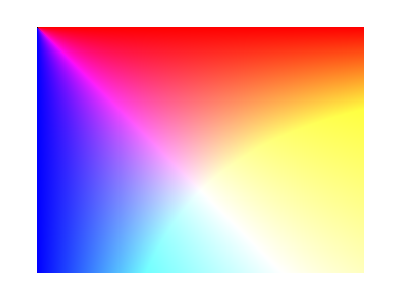

```mathematica
Clear[x,y,GetRGB];
ImgX=240;
ImgY=320;
(*GetRGB[x_,y_]:={Fitto1[x/(y+1)],Fitto1[(3 (x y))/(ImgX ImgY)],Fitto1[y/(x+1)]};*)
GetRGB=Compile[{{x,_Integer},{y,_Integer}},{Fitto1[x/(y+1)],Fitto1[(3 (x y))/(ImgX ImgY)],Fitto1[y/(x+1)]}];

gr=Show[Graphics[Raster[Table[GetRGB[y,ImgX-x],{x,0,ImgX,1},{y,0,ImgY,1}]]]]
```